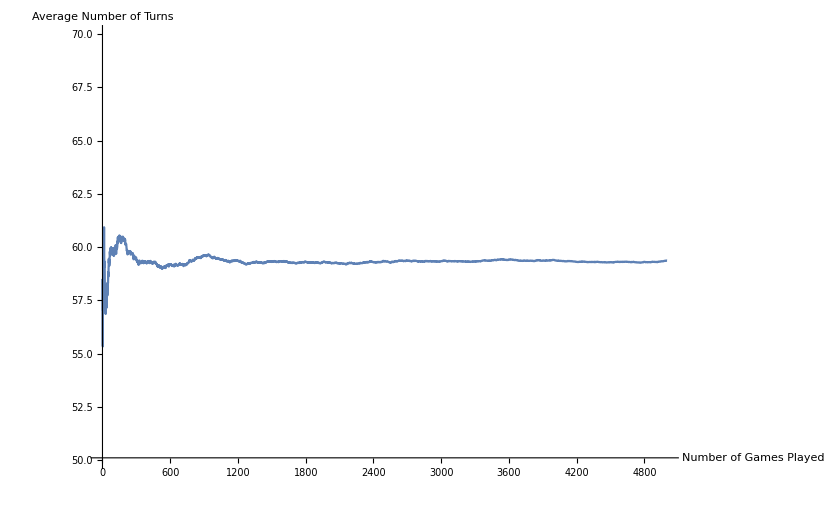

```mathematica
(* define initial conditions *)
star = 6;
players = 6;
iterations = 5000;

(* zero arrays *)
Array[x,players];
Array[aves,iterations];
For[q=1,q<iterations+ 1,q++,aves[q]=0];
ave = 0;
tot=0;

(* loop through a number of games and find the average game length*)
For[ct = 0,ct<iterations,ct++,
done = 0;
For[i=1,i<players + 1,i++,x[i]=star];
For[j=0,done <1,j++,
rolla = RandomInteger[{1,3}];
rollb = RandomInteger[{1,3}];
rollc = RandomInteger[{1,3}];

(* first rolled dice*)
If[x[Mod[j,players]+1]>0,
If[rolla ==2,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;,
If[rolla==1 && Mod[j,players] ≠ 0,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;
x[Mod[j,players]]= x[Mod[j,players]] +1;,
If[rolla ==1 && Mod[j,players] == 0,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;
x[players]]= x[players] + 1;,
If[rolla ==3 && Mod[j,players] ≠ players -1,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;
x[Mod[j,players] +2]= x[Mod[j,players]+2] +1;,
If[rolla ==3 && Mod[j,players] == players - 1,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;
x[1]= x[1] +1;
]
]
]
]
];
(* second rolled dice *)
If[x[Mod[j,players]+1]>1,
If[rollb==2,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;,
If[rollb ==1 && Mod[j,players] ≠ 0,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;
x[Mod[j,players]]= x[Mod[j,players]] +1;,
If[rollb ==1 && Mod[j,players] == 0,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;
x[players]]= x[players] + 1;,
If[rollb ==3 && Mod[j,players] ≠ players -1,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;
x[Mod[j,players] +2]= x[Mod[j,players]+2] +1;,
If[rollb ==3 && Mod[j,players] == players - 1,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;
x[1]= x[1] +1;
]
]
]
]
];

(* third rolled dice*)
If[x[Mod[j,players]+1]>2,
If[rollc ==2,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;,
If[rollc ==1 && Mod[j,players] ≠ 0,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;
x[Mod[j,players]]= x[Mod[j,players]] +1;,
If[rollc ==1 && Mod[j,players] == 0,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;
x[players]]= x[players] + 1;,
If[rollc ==3 && Mod[j,players] ≠ players -1,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;
x[Mod[j,players] +2]= x[Mod[j,players]+2] +1;,
If[rollc ==3 && Mod[j,players] == players - 1,
x[Mod[j,players]+1] = x[Mod[j,players]+1] -1;
x[1]= x[1] +1;
]
]
]
]
];

(*checks how many people are left, takes final answer if completed *)
losers = 0;
For[a =1,a<players + 1,a++,
If[x[a]==0,losers++]
]

If[losers ==players - 1,
done=1;
tot=tot+(j+1);
ave = tot/(ct +1);
aves[ct+1]=ave;] 

]
];

ListLinePlot[Table[{w+1,aves[w+1]},{w,1,iterations -1,1}],AxesLabel->{"Number of Games Played","Average Number of Turns"},PlotRange->{{0,5000},{50,70}}]
```